```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Robel\Desktop\Zhang\Code

```mathematica
len[s_]:= Length[s]
```

```mathematica
file = ""
data = Import[file][[1]]//ToExpression;
color = Import["color"<>file][[1]]//ToExpression;
groupgraph= Import["groups_"<>file][[1]]//ToExpression;
weigh= Import["group_weight_"<>file][[1]]//ToExpression;

grouplist = VertexList[Graph[groupgraph]];

colors = {Red,Blue,Green, Purple, Orange, Cyan, Magenta,Yellow,Brown, Gray};
Length[colors];
colorscheme = Table[i-1->colors[[Mod[color[[i]],10]+1]],{i, 1,len[color]}];
groupcolor = Table[grouplist[[i]]->colors[[Mod[grouplist[[i]],10]+1]],{i, 1,len[grouplist]}];

lable = Table[groupgraph[[i]]->weigh[[i]],{i, 1,len[weigh]}];
len[data]
```

robel.dat

1817

```mathematica
size = Large;
EdgeColor = Black;
vertsize = 1;
```

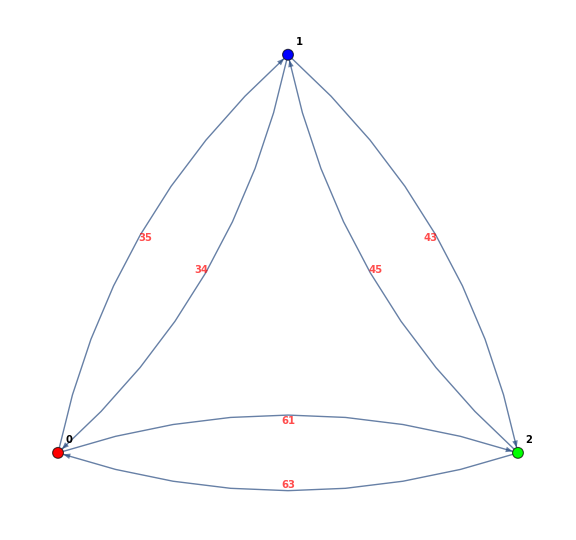

```mathematica
Graph[groupgraph,VertexStyle->groupcolor, VertexLabels->"Name",EdgeLabels->lable,
		VertexLabelStyle->Directive[Black,Bold,10],EdgeLabelStyle->Directive[Red,Bold,10],ImageSize->Large]
```

```mathematica
"Graph[data,VertexStyle→Black, EdgeStyle→EdgeColor,VertexSize→vertsize ,ImageSize→size];"
Graph[data,VertexStyle->colorscheme, EdgeStyle->EdgeColor,VertexSize->vertsize ,ImageSize->size]
```

Graph[data,VertexStyle→Black, EdgeStyle→EdgeColor,VertexSize→vertsize ,ImageSize→size];

-Graphics-

```mathematica
Graph3D[groupgraph,VertexStyle->groupcolor, VertexLabels->"Name",EdgeLabels->lable,EdgeStyle->Thick,
		VertexLabelStyle->Directive[Black,Bold,10],EdgeLabelStyle->Directive[Red,Bold,10],ImageSize->Large]
Graph3D[data,VertexStyle->colorscheme, EdgeStyle->EdgeColor,VertexSize->vertsize ,ImageSize->size];
```

-Graphics3D-

```mathematica
GraphPlot[data,ImageSize->size, VertexLabeling->True];
g1 = Graph[groupgraph,EdgeWeight->weigh];
```